# Attribution of Crop Production in United States of America Based on Artificial Neural Network

Yixuan Ma^(1,2), Baoxiang Pan^3

1. Beijing Jiaotong University
2. Department of Information and Computer Science, University of California, Irvine
3. Center for Hydrometeorology and Remote Sensing, University of California, Irvine

Abstract

Crop production in the United States of America takes a huge weight in international food supply and acts as pioneer in the evolution of modern agriculture. In order to better understand and improve crop productivity, a factor attribution analysis using artificial neural network was implemented based on the state crop production data and long term climate index records in 48 states across continent United States. Results showed that...

Introduction

Agriculture has been a fundamental organism of human society since the dawn of civilization. Despite its importance in providing food and work, the functioning of agriculture in different social stages takes different forms. Today in the United States of America, agriculture has been a major industry that produces the largest amount of exported crops that worth 118.3 billion dollars per year, coming from 2.2 million farms with an average area of 169 hectares for each farm[“US Census of Agriculture, 2007”. Agcensus.usda.gov. 2009-02-04. Retrieved 2014-04-01.].
    The prosperity of agriculture is dominated by many factors, including both climate and human impacts. The most important climate factors are precipitation and temperature variations. Human impact is consisted of international and national market, labor input, labor quality, nutrition input, fertilizer input, technical improvements, etc.. Different factors contribute differently to crop production in different regions. To attribute their specific contribution is of significant importance in understanding the hidden agricultural mechanism and providing useful information for improving productivity.
    While a purely physical simulation of crop cultivation is extremely difficult if not impossible, the carefully collected long record agricultural data offered an opportunity to build models and do analysis in a data-driven manner.  Data-driven models have been existing since Gauss applied the linear fitting for geometric measurements 200 years ago. In recent decades, both data and algorithm for data understanding are flourishing due to the arrival of electric computing era. Given the complexity of agriculture activities that involves both climate and human activity influences, linear models may not have the potential to satisfactorily re-project the input-output relationship. Researchers have been taking use of more complicated machine learning algorithms to simulate the crop production process. For example, Karimi applied support vector machine method to simulate the influence of weed and nitrogen on corn production in Canada[Karimi, Y., et al. “Application of support vector machine technology for weed and nitrogen stress detection in corn.” Computers and electronics in agriculture 51.1 (2006): 99-109.],  Wang etc.. used artificial neural network to evaluate land fertility.[Ruiyan, Wang, Zhao Gengxing, and Chen Lili. “Evaluation model of cultivated land fertility using artificial neural network and productivity and its application.” Transactions of the Chinese Society of Agricultural Engineering 2008.1 (2008).] Goel etc. compared the performance of decision tree algorithm and artificial neural network in identifying crop production factors[Goel, P. K., et al. “Classification of hyper spectral data by decision trees and artificial neural networks to identify weed stress and nitrogen status of corn.” Computers and Electronics in Agriculture 39.2 (2003): 67-93.]. 
    It should be noted that the performance of these data-driven models in the above research works have high requirement for sufficient, representative and accurate data. The related departments and associations in the United States of America act as good example for making clear and public reachable data for such research. The United States Department of Agriculture Economic Research Service(USDA)  have been collecting crop production data since 1960. With nearly 50 years of time series record of agriculture input and output variables in 48 states across the continent United States, we can set up data-driven models to reveal the mechanism that dominates the productivity of agriculture for each state. Besides, the National Center for Atmospheric Research have been providing climate records since its predecessor University Corporation for Atmospheric Research back in 1960th. Given the climate and human impact data collected from these corporations, we build  the artificial neural network(ANN) to model the influence of various factors on crop production in the continent United States. ANN was chosen for its strong simulating capacity and simple structure. With the model being set up and trained, we can quantitatively attribute the contribution of each factor on crop production for different states and make state wise comparisons. 
    To implement and illustrate this idea, the rest of the paper was organized as follows. The technical details of neural network structure, training strategy and performance evaluation was clarified in the second part. Data were introduced in the third part. The simulation of input-output relationship for crop cultivation was followed with factor attribution by tuning inputs in the fourth part. Discussion and conclusion were drawn at last.

Method

## Structure of Artificial Neural Network

ANN is a popular machine learning algorithm originated from the study of bio neural systems. It is consisted of layered graph with simple calculating units  as vertexes. The typical structure  of ANN is shown as follows:

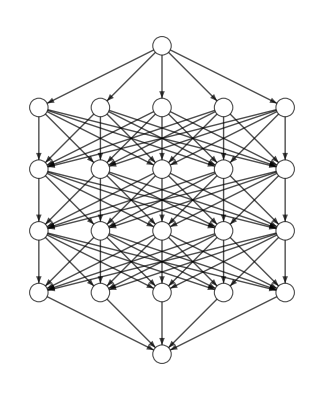
-Graphics-Figure 1. Typical Structure of Artificial Neural Network

```mathematica
Get["ANNPlot"];
Labeled[ANNPlot[{1,5,5,5,5,1}],"Figure 1. Typical Structure of Artificial Neural Network"]
```

Each vertex in the graph from Figure 1 is called “neuron”. In the biological neural system, neurons collect input excitements and generate respondent excitements, which will be transferred to subsequent neurons or muscle. In ANN, it squishes or stretches the input signal and generate respondent output signal. We can tune the parameters to twist the input-output relationship to match observations. ANN has been proven to be universal approximator[Hornik, Kurt, Maxwell Stinchcombe, and Halbert White. “Multilayer feedforward networks are universal approximators.” Neural networks 2.5 (1989): 359-366.], which means given enough layers with sufficient neurons, it has the capacity to simulate systems of arbitrary complexities.

## Using Back Propagation to Train ANN

The simulation capacity of ANN can only be realized with properly estimated parameters. The simple structure of feedforward neural network enables making calculus on its graph structure, which means we can calculate the gradient of its fitness function. The fitness function can be any function that captures the similarity between ANN simulations and observations, for example, it could be Euclidean distance, cross-entropy function, correlation coefficient, etc.. Each parameter, including the weights and biases for different input neurons and neuron activation function parameters, would be adjusted following the inverse direction of the gradient. The rate of the adjustment is called learning rate, which should be determine by trial and error. This parameter estimation strategy is called back propagation and has been widely used in ANN training since its discovery in the middle 1980th[Hecht-Nielsen, Robert. “Theory of the backpropagation neural network.” Neural Networks, 1989. IJCNN., International Joint Conference on. IEEE, 1989.]. To improve the speed of  training, sometimes only randomly-selected data batches were used to estimated the gradient. The learning rate was adjusted according to the performance improvement for each back propagation evolution. This strategy is named stochastic gradient descent using an adaptive learning rate(ADAM).

## Implementation

In this research work, ANN was implemented using the neural network module from Wolfram Mathematica 11[Wolfram Research, Inc., Mathematica, Version 11.0, Champaign, IL (2016).]. The specific structure of ANN was obtained through trial and error. To illustrate the importance of different categories of factors, 2 experiments were implemented based on a similar structured ANN:

```mathematica
Labeled[TableForm[{{"Experiment I","Human Influence Factors","Crop Production"},
		   {"Experiment II","Human Influence and Climate Factors","Crop Production"}},
		   TableHeadings->{None, {"No.","Input","Output"}}],"Table 1: Experiment Design",Top]
```

No. | Input | Output
Experiment I | Human Influence Factors | Crop Production
Experiment II | Human Influence and Climate Factors | Crop ProductionTable 1: Experiment Design

The attribution analysis were conducted according to the last experiment.

Data

Agricultural Data in this research were collected by the United States Department of Agriculture Economic Research Service. It applies a normalized  index to represent the agricultural productivity, which considered the quantities of commodities sold off the farm, additions to inventory, and quantities consumed as part of final demand in farm households during the calendar year. 12 agricultural variables were considered to be of significant influence on the crop production, which were introduced as follows:

```mathematica
InputVariableNames={"Total farm input by State",
			"Capital input",
			"Land input",
			"Total labor input",
			"Hired labor",
			"Self-employed and unpaid family labor",
			"Total intermediate input",
			"Energy input",
			"Agricultural chemical input",
			"Pesticide consumption",
			"Fertilizer consumption",
			"Other intermediate inputs"};
Labeled[TableForm[Table[{InputVariableNames[[i]],"lala"},{i,1,Length[InputVariableNames]}],
		  TableHeadings->{None,{"Variable", "Explanation"}}],"Table 2: Human Factors",Top]
```

Variable | Explanation
Total farm input by State | lala
Capital input | lala
Land input | lala
Total labor input | lala
Hired labor | lala
Self-employed and unpaid family labor | lala
Total intermediate input | lala
Energy input | lala
Agricultural chemical input | lala
Pesticide consumption | lala
Fertilizer consumption | lala
Other intermediate inputs | lalaTable 2: Human Factors

All the variables are state data and the record time ranges from 1960 to 2004. The time series plot of these variables were shown as follows:

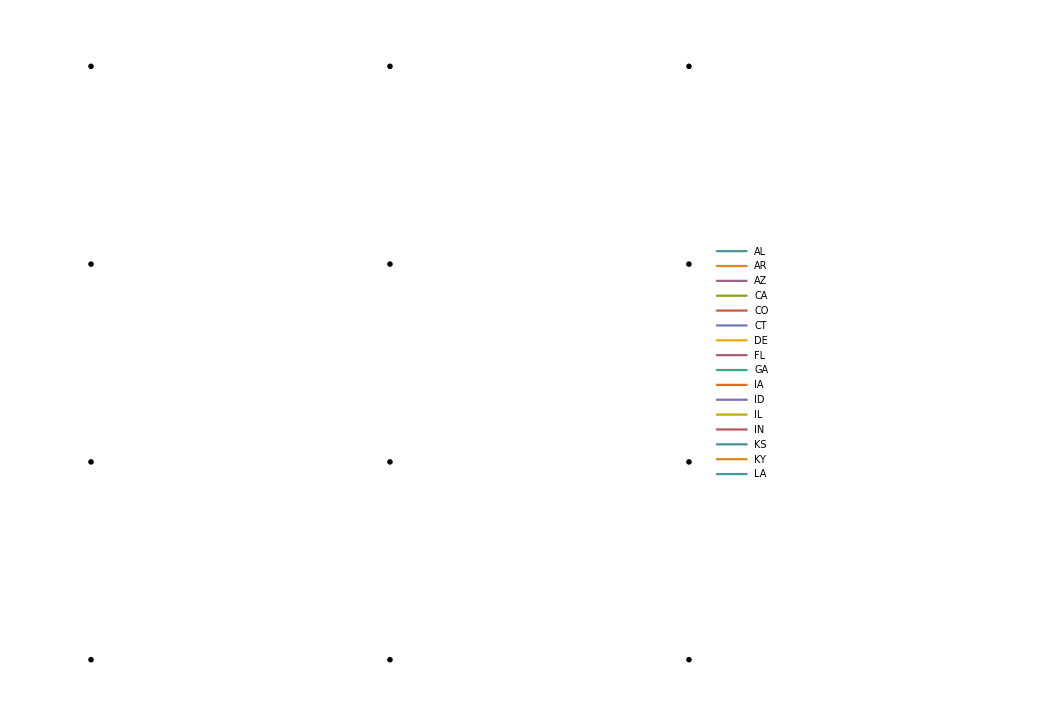

The crop production time series was shown as follows:

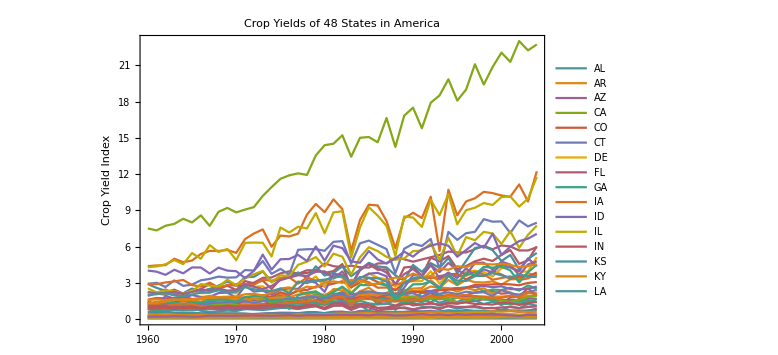

Beside the human impacts mentioned above, climate plays another significant role in crop cultivation. Although the improvement of agricultural techniques set a buffer for farms to go through certain level of climate extremes, such as flood or drought, heat or cold waves, it is quite important to  assess the relationship between climate variations and crop productions. Among all the climate variables, precipitation and temperature are two dominant factors. Here we adopted the monthly mean precipitation and temperature anomaly as climate factors for crop production simulation. They anomaly were obtained through subtracting the monthly mean value from the original monthly records and do spatial average for each state. The climate data information were listed as follows:

```mathematica
Labeled[TableForm[{{"Temperature","National Center for Environmental Prediction","1948-Present","2.5°×2.5°"},
		   {"Precipitation","Climate Prediction Center","1948-Present","0.25°×0.25°"}},
		   TableHeadings->{None, {"Variable","Provider","Temperal Converage","Spatial Resolution"}}],"Table 3: Climate Record Informaiton",Top]
```

Variable | Provider | Temperal Converage | Spatial Resolution
Temperature | National Center for Environmental Prediction | 1948-Present | 2.5°×2.5°
Precipitation | Climate Prediction Center | 1948-Present | 0.25°×0.25°Table 3: Climate Record Informaiton

Results

## Simulation

The ANN maps the input variables to the crop production index. Since all the agricultural data were normalized index data, they can be combined together as training and validation set. The first 33 years data from all 48 states were selected as parameter estimation set(training data size is 33×48=1584),  while leaving the last 12 years as validation set(validation data size is 12×48=576). The simulation performance measured in correlation coefficient and root mean square error for 2 experiments were depicted as follows:

```mathematica
TableForm[{{GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,1]],
	{i,1,48}],PlotRange->{0,1}],
		   GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,3]],
	{i,1,48}],PlotRange->{0,1}],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,1]],
	{i,1,48}],PlotRange->{0,1}],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,3]],
	{i,1,48}],PlotRange->{0,1}]},
		   {GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,2]],
	{i,1,48}],PlotRange->Automatic],
		   GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,4]],
	{i,1,48}],PlotRange->Automatic],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,2]],
	{i,1,48}],PlotRange->Automatic],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,4]],
	{i,1,48}],PlotRange->Automatic]}},
	TableHeadings->{{"ρ","RMSE"}, {"Estimation","Validation","Estimation","Validation"}},
	TableAlignments->Center]
```

| "Estimation" | "Validation" | "Estimation" | "Validation"
"ρ" | -Graphics- | -Graphics- | -Graphics- | -Graphics-
"RMSE" | -Graphics- | -Graphics- | -Graphics- | -Graphics-

For a clearer comparison of two experiments, the simulation result difference  were shown as follows:

```mathematica
TableForm[{{GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,1]]-statevalues2[[i,1]],
	{i,1,48}],PlotRange->{-0.25,0.25}],
GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,3]]-statevalues2[[i,3]],
	{i,1,48}],PlotRange->{-0.25,0.25}]},
		   {GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,2]]-statevalues2[[i,2]],
	{i,1,48}],PlotRange->Automatic],
	GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,4]]-statevalues2[[i,4]],
	{i,1,48}],PlotRange->{-0.,0.8}]}},
	TableHeadings->{{"ρ_I-ρ_II","RMSE_I-RMSE_II"}, {"Estimation","Validation"}},
	TableAlignments->Center]
```

| Estimation | Validation
ρ_I-ρ_II | -Graphics- | -Graphics-
RMSE_I-RMSE_II | -Graphics- | -Graphics-

## Factor Attribution

Discussion

Conclusion

```mathematica
TableForm[{{GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,1]],
	{i,1,48}],PlotRange->{0,1}],
		   GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,3]],
	{i,1,48}],PlotRange->{0,1}],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,1]],
	{i,1,48}],PlotRange->{0,1}],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,3]],
	{i,1,48}],PlotRange->{0,1}]},
		   {GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,2]],
	{i,1,48}],PlotRange->Automatic],
		   GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,4]],
	{i,1,48}],PlotRange->Automatic],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,2]],
	{i,1,48}],PlotRange->Automatic],
			GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues2[[i,4]],
	{i,1,48}],PlotRange->Automatic]}},
	TableHeadings->{{"ρ","RMSE"}, {"Estimation","Validation","Estimation","Validation"}},
	TableAlignments->Center]
```

# Attribution of Crop Production in United States of America Based on Artificial Neural Network

Yixuan Ma^(1,2), Baoxiang Pan^3

1. Beijing Jiaotong University
2. Department of Information and Computer Science, University of California, Irvine
3. Center for Hydrometeorology and Remote Sensing, University of California, Irvine

Abstract

Crop production in the United States of America takes a huge weight in international food supply and acts as pioneer in the evolution of modern agriculture. In order to better understand and improve crop productivity, a factor attribution analysis using artificial neural network was implemented based on the state crop production data and long term climate index records in 48 states across continent United States. Results showed that...

Introduction

Agriculture has been a fundamental organism of human society since the dawn of civilization. Despite its importance in providing food and work, the functioning of agriculture in different social stages takes different forms. Today in the United States of America, agriculture has been a major industry that produces the largest amount of exported crops that worth 118.3 billion dollars per year, coming from 2.2 million farms with an average area of 169 hectares for each farm[“US Census of Agriculture, 2007”. Agcensus.usda.gov. 2009-02-04. Retrieved 2014-04-01.].
    The prosperity of agriculture is dominated by many factors, including both climate and human impacts. The most important climate factors are precipitation and temperature variations. Human impact is consisted of international and national market, labor input, labor quality, nutrition input, fertilizer input, technical improvements, etc.. Different factors contribute differently to crop production in different regions. To attribute their specific contribution is of significant importance in understanding the hidden agricultural mechanism and providing useful information for improving productivity.
    While a purely physical simulation of crop cultivation is extremely difficult if not impossible, the carefully collected long record agricultural data offered an opportunity to build models and do analysis in a data-driven manner.  Data-driven models have been existing since Gauss applied the linear fitting for geometric measurements 200 years ago. In recent decades, both data and algorithm for data understanding are flourishing due to the arrival of electric computing era. Given the complexity of agriculture activities that involves both climate and human activity influences, linear models may not have the potential to satisfactorily re-project the input-output relationship. Researchers have been taking use of more complicated machine learning algorithms to simulate the crop production process. For example, Karimi applied support vector machine method to simulate the influence of weed and nitrogen on corn production in Canada[Karimi, Y., et al. “Application of support vector machine technology for weed and nitrogen stress detection in corn.” Computers and electronics in agriculture 51.1 (2006): 99-109.],  Wang etc.. used artificial neural network to evaluate land fertility.[Ruiyan, Wang, Zhao Gengxing, and Chen Lili. “Evaluation model of cultivated land fertility using artificial neural network and productivity and its application.” Transactions of the Chinese Society of Agricultural Engineering 2008.1 (2008).] Goel etc. compared the performance of decision tree algorithm and artificial neural network in identifying crop production factors[Goel, P. K., et al. “Classification of hyper spectral data by decision trees and artificial neural networks to identify weed stress and nitrogen status of corn.” Computers and Electronics in Agriculture 39.2 (2003): 67-93.]. 
    It should be noted that the performance of these data-driven models in the above research works have high requirement for sufficient, representative and accurate data. The related departments and associations in the United States of America act as good example for making clear and public reachable data for such research. The United States Department of Agriculture Economic Research Service(USDA)  have been collecting crop production data since 1960. With nearly 50 years of time series record of agriculture input and output variables in 48 states across the continent United States, we can set up data-driven models to reveal the mechanism that dominates the productivity of agriculture for each state. Besides, the National Center for Atmospheric Research have been providing climate records since its predecessor University Corporation for Atmospheric Research back in 1960th. Given the climate and human impact data collected from these corporations, we build  the artificial neural network(ANN) to model the influence of various factors on crop production in the continent United States. ANN was chosen for its strong simulating capacity and simple structure. With the model being set up and trained, we can quantitatively attribute the contribution of each factor on crop production for different states and make state wise comparisons. 
    To implement and illustrate this idea, the rest of the paper was organized as follows. The technical details of neural network structure, training strategy and performance evaluation was clarified in the second part. Data were introduced in the third part. The simulation of input-output relationship for crop cultivation was followed with factor attribution by tuning inputs in the fourth part. Discussion and conclusion were drawn at last.

Method

## Structure of Artificial Neural Network

ANN is a popular machine learning algorithm originated from the study of bio neural systems. It is consisted of layered graph with simple calculating units  as vertexes. The typical structure  of ANN is shown as follows:

```mathematica
Get["ANNPlot"];
Labeled[ANNPlot[{1,5,5,5,5,1}],"Figure 1. Typical Structure of Artificial Neural Network"]
```

-Graphics-Figure 1. Typical Structure of Artificial Neural Network

Each vertex in the graph from Figure 1 is called “neuron”. In the biological neural system, neurons collect input excitements and generate respondent excitements, which will be transferred to subsequent neurons or muscle. In ANN, it squishes or stretches the input signal and generate respondent output signal. We can tune the parameters to twist the input-output relationship to match observations. ANN has been proven to be universal approximator[Hornik, Kurt, Maxwell Stinchcombe, and Halbert White. “Multilayer feedforward networks are universal approximators.” Neural networks 2.5 (1989): 359-366.], which means given enough layers with sufficient neurons, it has the capacity to simulate systems of arbitrary complexities.

## Using Back Propagation to Train ANN

The simulation capacity of ANN can only be realized with properly estimated parameters. The simple structure of feedforward neural network enables making calculus on its graph structure, which means we can calculate the gradient of its fitness function. The fitness function can be any function that captures the similarity between ANN simulations and observations, for example, it could be Euclidean distance, cross-entropy function, correlation coefficient, etc.. Each parameter, including the weights and biases for different input neurons and neuron activation function parameters, would be adjusted following the inverse direction of the gradient. The rate of the adjustment is called learning rate, which should be determine by trial and error. This parameter estimation strategy is called back propagation and has been widely used in ANN training since its discovery in the middle 1980th[Hecht-Nielsen, Robert. “Theory of the backpropagation neural network.” Neural Networks, 1989. IJCNN., International Joint Conference on. IEEE, 1989.]. To improve the speed of  training, sometimes only randomly-selected data batches were used to estimated the gradient. The learning rate was adjusted according to the performance improvement for each back propagation evolution. This strategy is named stochastic gradient descent using an adaptive learning rate(ADAM).

## Implementation

In this research work, ANN was implemented using the neural network module from Wolfram Mathematica 11[Wolfram Research, Inc., Mathematica, Version 11.0, Champaign, IL (2016).]. The specific structure of ANN was obtained through trial and error. To illustrate the importance of different categories of factors, 2 experiments were implemented based on a similar structured ANN:

```mathematica
Labeled[TableForm[{{"Experiment I","Human Influence Factors","Crop Production"},
		   {"Experiment II","Human Influence and Climate Factors","Crop Production"}},
		   TableHeadings->{None, {"No.","Input","Output"}}],"Table 1: Experiment Design",Top]
```

No. | Input | Output
Experiment I | Human Influence Factors | Crop Production
Experiment II | Human Influence and Climate Factors | Crop ProductionTable 1: Experiment Design

The attribution analysis were conducted according to the last experiment.

Data

Agricultural Data in this research were collected by the United States Department of Agriculture Economic Research Service. It applies a normalized  index to represent the agricultural productivity, which considered the quantities of commodities sold off the farm, additions to inventory, and quantities consumed as part of final demand in farm households during the calendar year. 12 agricultural variables were considered to be of significant influence on the crop production, which were introduced as follows:

```mathematica
InputVariableNames={"Total farm input by State",
			"Capital input",
			"Land input",
			"Total labor input",
			"Hired labor",
			"Self-employed and unpaid family labor",
			"Total intermediate input",
			"Energy input",
			"Agricultural chemical input",
			"Pesticide consumption",
			"Fertilizer consumption",
			"Other intermediate inputs"};
Labeled[TableForm[Table[{InputVariableNames[[i]],"lala"},{i,1,Length[InputVariableNames]}],
		  TableHeadings->{None,{"Variable", "Explanation"}}],"Table 2: Human Factors",Top]
```

Variable | Explanation
Total farm input by State | lala
Capital input | lala
Land input | lala
Total labor input | lala
Hired labor | lala
Self-employed and unpaid family labor | lala
Total intermediate input | lala
Energy input | lala
Agricultural chemical input | lala
Pesticide consumption | lala
Fertilizer consumption | lala
Other intermediate inputs | lalaTable 2: Human Factors

All the variables are state data and the record time ranges from 1960 to 2004. The time series plot of these variables were shown as follows:

-Graphics-

The crop production time series was shown as follows:

-Graphics-

Beside the human impacts mentioned above, climate plays another significant role in crop cultivation. Although the improvement of agricultural techniques set a buffer for farms to go through certain level of climate extremes, such as flood or drought, heat or cold waves, it is quite important to  assess the relationship between climate variations and crop productions. Among all the climate variables, precipitation and temperature are two dominant factors. Here we adopted the monthly mean precipitation and temperature anomaly as climate factors for crop production simulation. They anomaly were obtained through subtracting the monthly mean value from the original monthly records and do spatial average for each state. The climate data information were listed as follows:

```mathematica
Labeled[TableForm[{{"Temperature","National Center for Environmental Prediction","1948-Present","2.5°×2.5°"},
		   {"Precipitation","Climate Prediction Center","1948-Present","0.25°×0.25°"}},
		   TableHeadings->{None, {"Variable","Provider","Temperal Converage","Spatial Resolution"}}],"Table 3: Climate Record Informaiton",Top]
```

Variable | Provider | Temperal Converage | Spatial Resolution
Temperature | National Center for Environmental Prediction | 1948-Present | 2.5°×2.5°
Precipitation | Climate Prediction Center | 1948-Present | 0.25°×0.25°Table 3: Climate Record Informaiton

Results

## Simulation

The ANN maps the input variables to the crop production index. Since all the agricultural data were normalized index data, they can be combined together as training and validation set. The first 33 years data from all 48 states were selected as parameter estimation set(training data size is 33×48=1584),  while leaving the last 12 years as validation set(validation data size is 12×48=576). The simulation performance measured in correlation coefficient and root mean square error for 2 experiments were depicted as follows:

```mathematica
TableForm[{{GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues1[[i, 1]],
     	{i, 1, 48}], PlotRange -> {0, 1}],
   		   GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues1[[i, 3]],
     	{i, 1, 48}], PlotRange -> {0, 1}],
   			GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues2[[i, 1]],
     	{i, 1, 48}], PlotRange -> {0, 1}],
   			GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues2[[i, 3]],
     	{i, 1, 48}], PlotRange -> {0, 1}]},
  		   {GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues1[[i, 2]],
     	{i, 1, 48}], PlotRange -> Automatic],
   		   GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues1[[i, 4]],
     	{i, 1, 48}], PlotRange -> Automatic],
   			GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues2[[i, 2]],
     	{i, 1, 48}], PlotRange -> Automatic],
   			GeoRegionValuePlot[
    		Table[StateFullName[[i]] -> statevalues2[[i, 4]],
     	{i, 1, 48}], PlotRange -> Automatic]}},
 	TableHeadings -> {{"ρ", "RMSE"}, {"Estimation_I", "Validation_I", "Estimation_II", "Validation_II"}},
 	TableAlignments -> Center]
```

| Estimation_I | Validation_I | Estimation_II | Validation_II
ρ | -Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE | -Graphics- | -Graphics- | -Graphics- | -Graphics-

For a clearer comparison of two experiments, the simulation result difference  were shown as follows:

```mathematica
TableForm[{{GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,1]]-statevalues2[[i,1]],
	{i,1,48}],PlotRange->{-0.25,0.25}],
GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,3]]-statevalues2[[i,3]],
	{i,1,48}],PlotRange->{-0.25,0.25}]},
		   {GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,2]]-statevalues2[[i,2]],
	{i,1,48}],PlotRange->Automatic],
	GeoRegionValuePlot[
		Table[StateFullName[[i]]->statevalues1[[i,4]]-statevalues2[[i,4]],
	{i,1,48}],PlotRange->{-0.,0.8}]}},
	TableHeadings->{{"ρ_I-ρ_II","RMSE_I-RMSE_II"}, {"Estimation","Validation"}},
	TableAlignments->Center]
```

| Estimation | Validation
ρ_I-ρ_II | -Graphics- | -Graphics-
RMSE_I-RMSE_II | -Graphics- | -Graphics-

## Factor Attribution

Discussion

Conclusion